```mathematica
ClearAll["Global`*"]
```

```mathematica
E2a[n_,k_, a_]:= E2a[n,k,a]=Sum[ E2a[n/j,k-1,a],{j,2,n}]-a Sum[ E2a[n/(a j),k-1,a],{j,1,n/a}];E2a[n_,0,a_]:=1
E2D2[n_,k_,b_]:= (-1)^k+Sum[b^a/((k-1)!) Binomial[k,j]Pochhammer[a-k+j+1,k-1]E2a[b^-a n,j,b],{a,0,Log[b,n]},{j,0,k}]
D2a[n_,k_]:=D2a[n,k]=Sum[D2a[Floor[n/j],k-1],{j,2,n}];D2a[n_,0]:=1
d2[n_,k_]:=Sum[d2[j,k-1] d2[n/j,1],{j,Divisors[n]}];d2[n_,1]:=1;d2[1,1]:=0;d2[n_,0]:=0;d2[1,0]:=1
bin[n_,k_] := (n)!/((k!)((n-k)!))
```

```mathematica
D2a[100,2]
```

283

```mathematica
E2D2[100,2,11/10]
```

283

```mathematica
E2D2a[n_,k_,a_]:= (-1)^k+Sum[a^j/((k-1)!) Binomial[k,m]Pochhammer[j-k+m+1,k-1]E2a[a^-j n,m,a],{j,0,Log[a,n]},{m,0,k}]
```

```mathematica
E2D2a[100,3,3/2]
```

324

```mathematica
E2D2b[n_,k_,a_]:= (-1)^k+Sum[a^j Binomial[k,m]Pochhammer[j-k+m+1,k-1]E2a[a^-j n,m,a],{j,0,Log[a,n]},{m,0,k}]/Gamma[k]
```

```mathematica
E2D2b[100,3,3/2]
```

324

```mathematica
E2D2c[n_,k_,a_]:= (-1)^k+Sum[a^j Sum[ Binomial[k,m]Pochhammer[j-k+m+1,k-1]E2a[a^-j n,m,a],{m,0,k}],{j,0,Log[a,n]}]/Gamma[k]
```

```mathematica
E2D2c[100,3,3/2]
```

324

```mathematica
(-1)^k+Sum[a^j Sum[ Binomial[k,m]Pochhammer[j-k+m+1,k-1]E2[a^-j n,m,a],{m,0,k}],{j,0,Log[a,n]}]/Gamma[k]/.k->1
```

-1+∑_(j=0)^(Log[n]/Log[a]) a^j (E2[a^-j n,0,a]+E2[a^-j n,1,a])

```mathematica
(-1)^k+Sum[a^j Sum[ Binomial[k,m]Pochhammer[j-k+m+1,k-1]E2[a^-j n,m,a],{m,0,k}],{j,0,Log[a,n]}]/Gamma[k]/.k->2
```

1+∑_(j=0)^(Log[n]/Log[a]) a^j ((-1+j) E2[a^-j n,0,a]+2 j E2[a^-j n,1,a]+(1+j) E2[a^-j n,2,a])

```mathematica
(-1)^k+Sum[a^j Sum[ Binomial[k,m]Pochhammer[j-k+m+1,k-1]E2[a^-j n,m,a],{m,0,k}],{j,0,Log[a,n]}]/Gamma[k]/.k->3
```

-1+1/2 ∑_(j=0)^(Log[n]/Log[a]) a^j ((-2+j) (-1+j) E2[a^-j n,0,a]+3 (-1+j) j E2[a^-j n,1,a]+3 j (1+j) E2[a^-j n,2,a]+(1+j) (2+j) E2[a^-j n,3,a])

```mathematica
(-1)^k+Sum[a^j Sum[ Binomial[k,m]Pochhammer[j-k+m+1,k-1]E2[a^-j n,m,a],{m,0,k}],{j,0,Log[a,n]}]/Gamma[k]/.k->4
```

```mathematica
f[n_,a_]:=1+∑_(j=0)^(Log[n]/Log[a]) a^j j (a-1)^2
```

```mathematica
f[100,1.01]
```

364.674

```mathematica
N[Gamma[2,0,-Log[100]]]
```

361.517-4.41506×10^-14 ⅈ

```mathematica
g[n_, a_] := Sum[ a^j (a-1)^2 (-1)^2 j,{j,1,Log[a,n]}]
```

```mathematica
D2a[100,2]-g[100,1.0001]
```

-78.576

```mathematica
E2D2d[n_,k_,a_]:= (-1)^k+Sum[a^j( -j^(k-1)(a-1)^k+ Sum[ Binomial[k,m]Pochhammer[j-k+m+1,k-1]E2a[a^-j n,m,a],{m,0,k}]),{j,0,Log[a,n]}]/Gamma[k]
```

```mathematica
E2D2d[100,2,1.001]
```

-78.8913

-78.517+4.41506×10^-14 ⅈ

```mathematica
E2D2e[n_,k_,a_]:= (-1)^k+Sum[a^j( -(j^(k-1)(a-1)^k)+ Sum[ Binomial[k,m]Pochhammer[j-k+m+1,k-1]E2[a^-j n,m,a],{m,0,k}]),{j,0,Log[a,n]}]/Gamma[k]
```

```mathematica
Expand[( -((a-1)^k))]
```

-(-1+a)^k

```mathematica
E2D2e[n,2,a]
```

1+∑_(j=0)^(Log[n]/Log[a]) a^j (-(-1+a)^2 j+(-1+j) E2[a^-j n,0,a]+2 j E2[a^-j n,1,a]+(1+j) E2[a^-j n,2,a])

```mathematica
E2D2e[n,3,a]
```

-1+1/2 ∑_(j=0)^(Log[n]/Log[a]) a^j (-(-1+a)^3 j^2+(-2+j) (-1+j) E2[a^-j n,0,a]+3 (-1+j) j E2[a^-j n,1,a]+3 j (1+j) E2[a^-j n,2,a]+(1+j) (2+j) E2[a^-j n,3,a])

```mathematica
E2D2f[n_,k_,a_]:= (-1)^k+Sum[a^j j^(k-1)( -(a-1)^k+ Sum[ Binomial[k,m](Pochhammer[j-k+m+1,k-1]/j^(k-1))E2[a^-j n,m,a],{m,0,k}]),{j,0,Log[a,n]}]/Gamma[k]
```

```mathematica
E2D2f[n,2,a]
```

1+∑_(j=0)^(Log[n]/Log[a]) a^j j (-(-1+a)^2+((-1+j) E2[a^-j n,0,a])/j+2 E2[a^-j n,1,a]+((1+j) E2[a^-j n,2,a])/j)

```mathematica
E2D2f[n,3,a]
```

-1+1/2 ∑_(j=0)^(Log[n]/Log[a]) a^j j^2 (-(-1+a)^3+((-2+j) (-1+j) E2[a^-j n,0,a])/j^2+(3 (-1+j) E2[a^-j n,1,a])/j+(3 (1+j) E2[a^-j n,2,a])/j+((1+j) (2+j) E2[a^-j n,3,a])/j^2)

```mathematica
Expand[(a-1)^3]
```

-1+3 a-3 a^2+a^3

```mathematica
E2D2g[n_,k_,a_]:= (-1)^k+Sum[a^j j^(k-1)( Sum[ Binomial[k,m](Pochhammer[j-k+m+1,k-1]/j^(k-1))(E2a[a^-j n,m,a]-(Binomial[k,m]a^m)),{m,0,k}]),{j,1,Log[a,n]}]/Gamma[k]
```

```mathematica
E2D2g[n,3,a]
```

-1+1/(2 (-1+a)^3 Log[a]^2)(38 a^3 Log[a]^2+6 a^4 Log[a]^2-6 a^5 Log[a]^2+2 a^6 Log[a]^2-38 a^3 n Log[a]^2-6 a^4 n Log[a]^2+6 a^5 n Log[a]^2-2 a^6 n Log[a]^2+a n Log[a] Log[n]-13 a^2 n Log[a] Log[n]-24 a^3 n Log[a] Log[n]+40 a^4 n Log[a] Log[n]-a^5 n Log[a] Log[n]-3 a^6 n Log[a] Log[n]-a n Log[n]^2-7 a^2 n Log[n]^2+8 a^3 n Log[n]^2+8 a^4 n Log[n]^2-7 a^5 n Log[n]^2-a^6 n Log[n]^2)

```mathematica
E2D2g[100,3,2]
```

-122001

```mathematica
E2D2h[n_,k_,a_]:= 
(-1)^k+Sum[

a^j(

 -j^(k-1)(a-1)^k

+
 Sum[ 

(Binomial[k,m]Pochhammer[j-k+m+1,k-1]E2a[a^-j n,m,a])

,{m,0,k}]),{j,0,Log[a,n]}]/Gamma[k]
```

```mathematica
E2D2h[100,2,1.001]
```

-78.8913

```mathematica
E2D2i[n_,k_,a_]:= 
(-1)^k+Sum[

a^j(




 Sum[ 
Binomial[k,m]
(Pochhammer[j-k+m+1,k-1]E2a[a^-j n,m,a]
-j^(k-1)(a^m (-1)^(k-m))
)

,{m,0,k}]),{j,0,Log[a,n]}]/Gamma[k]
```

```mathematica
E2D2i[50,2,1.001]
```

-38.6541

```mathematica
D2a[50,2]-g[50,1.0001]
```

-38.622

```mathematica
fe1[j_,k_,a_]:=(a-1)^k
```

```mathematica
Expand[fe1[3,4,a]]
```

1-4 a+6 a^2-4 a^3+a^4

```mathematica
fe2[j_,k_,a_]:=Sum[Binomial[k,s]a^s (-1)^(k-s),{s,0,k}]
```

```mathematica
fe2[3,4,a]
```

1-4 a+6 a^2-4 a^3+a^4

```mathematica
E2D2j[n_,k_,a_]:=(-1)^k+Sum[a^j(Sum[ Binomial[k,m](Pochhammer[j-k+m+1,k-1]E2a[a^-j n,m,a]-j^(k-1)(a^m (-1)^(k-m))),{m,0,k}]),{j,0,Log[a,n]}]/Gamma[k]
```

```mathematica
E2D2j[50,2,1.001]
```

-38.6541

```mathematica
N[D2a[50,2]-Gamma[2,0,-Log[50]]/Gamma[2]]
```

-38.6012+1.7831×10^-14 ⅈ

```mathematica
a^j(Sum[ Binomial[k,m](Pochhammer[j-k+m+1,k-1]E2[a^-j n,m,a]-j^(k-1)(a^m (-1)^(k-m))),{m,0,k}])/.j->0
```

$Aborted

```mathematica
FullSimplify[Pochhammer[j-k+m+1,k-1]E2[a^-j n,m,a]-j^(k-1)(a^m (-1)^(k-m))]
```

-(-1)^(k-m) a^m j^(-1+k)+E2[a^-j n,m,a] Pochhammer[1+j-k+m,-1+k]

```mathematica
Gamma[(1+j-k+m)+1]/Gamma[(1+j-k+m)-(-1+k)+1]
```

Gamma[2+j-k+m]/Gamma[3+j-2 k+m]

```mathematica
FullSimplify[Gamma[j+m]/Gamma[-1+k] E2[a^-j n,m,a]-j^(k-1)(a^m (-1)^(k-m))]
```

-(-1)^(k-m) a^m j^(-1+k)+(E2[a^-j n,m,a] Gamma[j+m])/Gamma[-1+k]

```mathematica
E2D2k[n_,k_,a_]:=(-1)^k+Sum[a^j(Sum[ Binomial[k,m](Gamma[j+m]/Gamma[1+j-k+m] E2a[a^-j n,m,a]-j^(k-1)(a^m (-1)^(k-m))),{m,0,k}]),{j,0,Log[a,n]}]/Gamma[k]
```

```mathematica
E2D2k[50,2,1.001]
```

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Indeterminate

```mathematica
bb[j_,k_,m_]:= Pochhammer[j-k+m+1,k-1]
```

```mathematica
bb[3,4,5]
```

210

```mathematica
bb2[j_,k_,m_]:=Gamma[(j-k+m+1)+(k-1)]/Gamma[(j-k+m+1)]
```

```mathematica
bb2[3,4,5]
```

210

```mathematica
bb3[j_,k_,m_]:=Binomial[j-k+m+1+(k-1)-1,k-1]((k-1)!)
```

```mathematica
bb3[3,4,5]
```

210

```mathematica
Gamma[(j-k+m+1)+(k-1)]/Gamma[(j-k+m+1)]
```

Gamma[j+m]/Gamma[1+j-k+m]

```mathematica
bb4[j_,k_,m_]:=Binomial[j-k+m+1+(k-1)-1,k-1]((k-1)!)
```

```mathematica
bb4[3,4,5]
```

210

```mathematica
bin[n_,k_] := (n)!/((k!)((n-k)!))
```

```mathematica
bb5[j_,k_,m_]:=bin[j-k+m+1+(k-1)-1,k-1]((k-1)!)
```

```mathematica
bb5[3,4,5]
```

210

```mathematica
bin[j-k+m+1+(k-1)-1,k-1]((k-1)!)
```

```mathematica
((-1+j+m)!)/((j-k+m)!)
```

((-1+j+m)!)/((j-k+m)!)

```mathematica
E2D2j[n_,k_,a_]:=(-1)^k+
(a^0(Sum[ Binomial[k,m](Pochhammer[0-k+m+1,k-1]E2a[a^-0 n,m,a]-0^(k-1)(a^m (-1)^(k-m))),{m,0,k}])+
Sum[a^j(Sum[ Binomial[k,m](Pochhammer[j-k+m+1,k-1]E2a[a^-j n,m,a]-j^(k-1)(a^m (-1)^(k-m))),{m,0,k}]),{j,1,Log[a,n]}])/Gamma[k]
```

```mathematica
E2D2j[100,2,1.001]
```

-78.8913

```mathematica
E2D2k[n_,k_,a_]:=(-1)^k+
((Sum[ Binomial[k,m](Pochhammer[-k+m+1,k-1]E2a[a^-0 n,m,a]-(a^m (-1)^(k-m))),{m,0,k}])+
Sum[a^j(Sum[ Binomial[k,m](Pochhammer[j-k+m+1,k-1]E2a[a^-j n,m,a]-j^(k-1)(a^m (-1)^(k-m))),{m,0,k}]),{j,1,Log[a,n]}])/Gamma[k]
```

```mathematica
E2D2k[100,2,1.001]
```

-78.8913

```mathematica
E2D2m[n_,k_,a_]:=(-1)^k+
((Sum[ Binomial[k,m](Pochhammer[-k+m+1,k-1]E2a[n,m,a]-(a^m (-1)^(k-m))),{m,0,k}])+
Sum[a^j(Sum[ Binomial[k,m](Pochhammer[j-k+m+1,k-1]E2a[a^-j n,m,a]-j^(k-1)(a^m (-1)^(k-m))),{m,0,k}]),{j,1,Log[a,n]}])/Gamma[k]
```

```mathematica
E2D2m[100,2,1.001]
```

-78.8913

```mathematica
Pochhammer[-k+m+1,k-1]/.{m->1,k->5}
```

0

```mathematica
E2D2n[n_,k_,a_]:=(-1)^k+
((Sum[ Binomial[k,m](Pochhammer[-k+m+1,k-1]E2a[n,m,a]),{m,0,k}])+
(Sum[ Binomial[k,m](-(a^m (-1)^(k-m))),{m,0,k}])+
Sum[a^j(Sum[ Binomial[k,m](Pochhammer[j-k+m+1,k-1]E2a[a^-j n,m,a]-j^(k-1)(a^m (-1)^(k-m))),{m,0,k}]),{j,1,Log[a,n]}])/Gamma[k]
```

```mathematica
E2D2n[100,2,1.001]
```

-78.8913

```mathematica
E2D2o[n_,k_,a_]:=(-1)^k+
((Sum[ (Pochhammer[-k+m+1,k-1]E2a[n,m,a]),{m,0,0}])+
Sum[ (Pochhammer[-k+m+1,k-1]E2a[n,m,a]),{m,k,k}]+
(Sum[ Binomial[k,m](-(a^m (-1)^(k-m))),{m,0,k}])+
Sum[a^j(Sum[ Binomial[k,m](Pochhammer[j-k+m+1,k-1]E2a[a^-j n,m,a]-j^(k-1)(a^m (-1)^(k-m))),{m,0,k}]),{j,1,Log[a,n]}])/Gamma[k]
```

```mathematica
E2D2o[100,2,1.001]
```

-78.8913

```mathematica
E2D2p[n_,k_,a_]:=(-1)^k+
(
Pochhammer[-k+1,k-1]E2a[n,0,a]+
 Pochhammer[-k+k+1,k-1]E2a[n,k,a]+
(Sum[ Binomial[k,m](-(a^m (-1)^(k-m))),{m,0,k}])+
Sum[a^j(Sum[ Binomial[k,m](Pochhammer[j-k+m+1,k-1]E2a[a^-j n,m,a]-j^(k-1)(a^m (-1)^(k-m))),{m,0,k}]),{j,1,Log[a,n]}])/Gamma[k]
```

```mathematica
E2D2p[100,2,1.001]
```

-78.8913

```mathematica
E2D2q[n_,k_,a_]:=(-1)^k+
((-1)^(k+1)Gamma[k]E2a[n,0,a]+
Gamma[k] E2a[n,k,a]+
(Sum[ Binomial[k,m](-(a^m (-1)^(k-m))),{m,0,k}])+
Sum[a^j(Sum[ Binomial[k,m](Pochhammer[j-k+m+1,k-1]E2a[a^-j n,m,a]-j^(k-1)(a^m (-1)^(k-m))),{m,0,k}]),{j,1,Log[a,n]}])/Gamma[k]
```

```mathematica
E2D2q[100,2,1.001]
```

-78.8913

```mathematica
Pochhammer[1-5,5-1]
```

24

```mathematica
(-1)^(k+1)Gamma[k]/.k->5
```

24

```mathematica
Pochhammer[1,4-1]
```

6

```mathematica
E2D2r[n_,k_,a_]:=(-1)^k+(-1)^(k+1)E2a[n,0,a]+ E2a[n,k,a]+(
(Sum[ Binomial[k,m](-(a^m (-1)^(k-m))),{m,0,k}])+
Sum[a^j(Sum[ Binomial[k,m](Pochhammer[j-k+m+1,k-1]E2a[a^-j n,m,a]-j^(k-1)(a^m (-1)^(k-m))),{m,0,k}]),{j,1,Log[a,n]}])/Gamma[k]
```

```mathematica
E2D2r[100,2,1.001]
```

-78.8913

```mathematica
E2D2s[n_,k_,a_]:= E2a[n,k,a]+(
(Sum[ Binomial[k,m](-(a^m (-1)^(k-m))),{m,0,k}])+
Sum[a^j(Sum[ Binomial[k,m](Pochhammer[j-k+m+1,k-1]E2a[a^-j n,m,a]-j^(k-1)(a^m (-1)^(k-m))),{m,0,k}]),{j,1,Log[a,n]}])/Gamma[k]
```

```mathematica
E2D2s[100,2,1.001]
```

-78.8913

```mathematica
pp[k_,a_]:=Sum[ Binomial[k,m](-(a^m (-1)^(k-m))),{m,0,k}]
```

```mathematica
pp[2,1.001]
```

-1.×10^-6

```mathematica
E2D2t[n_,k_,a_]:= E2a[n,k,a]+(
Sum[a^j(Sum[ Binomial[k,m](Pochhammer[j-k+m+1,k-1]E2a[a^-j n,m,a]-j^(k-1)(a^m (-1)^(k-m))),{m,0,k}]),{j,1,Log[a,n]}])/Gamma[k]
```

```mathematica
E2D2t[100,2,1.001]
```

-78.8913

```mathematica
{E2a[8,2,1.0001],d2[8,2]+1}
```

{3.0014,3}

```mathematica
{E2a[12,3,1.0001],d2[12,3]-1}
```

{1.9967,2}

```mathematica
{E2a[64,5,1.0001],d2[64,5]-1}
```

{3.96847,4}

```mathematica
E2D2u[n_,k_,a_]:= d2[n,k] + (-1)^(k)+(
Sum[a^j(Sum[ Binomial[k,m](Pochhammer[j-k+m+1,k-1]E2a[a^-j n,m,a]-j^(k-1)(a^m (-1)^(k-m))),{m,0,k}]),{j,1,Log[a,n]}])/Gamma[k]
```

```mathematica
E2D2u[100,2,1.001]
```

-79.0897

```mathematica
E2D2v[n_,k_,a_]:= d2[n,k] + (-1)^(k)+(Sum[a^j(Sum[ Binomial[k,m]((((-1+j+m)!)/((j-k+m)!))E2a[a^-j n,m,a]-j^(k-1)(a^m (-1)^(k-m))),{m,0,k}]),{j,1,Log[a,n]}])/Gamma[k]
```

```mathematica
E2D2v[100,2,1.001]
```

-79.0897

```mathematica
E2D2w[n_,k_,a_]:= d2[n,k] + (-1)^(k)+(Sum[a^j j^(k-1)(Sum[ Binomial[k,m]((((-1+j+m)!)/((j-k+m)!))/(j^(k-1))E2a[a^-j n,m,a]-(a^m (-1)^(k-m))),{m,0,k}]),{j,1,Log[a,n]}])/Gamma[k]
```

```mathematica
E2D2w[100,2,1.001]
```

-79.0897

```mathematica
E2D2x[n_,k_,a_]:= d2[n,k] + (-1)^(k)+(Sum[a^j j^(k-1)(Sum[ Binomial[k,m]((j^(1-k) Binomial[-1+j+m,-1+k] )E2a[a^-j n,m,a]-(a^m (-1)^(k-m))/Gamma[k]),{m,0,k}]),{j,1,Log[a,n]}])
```

```mathematica
E2D2x[100,2,1.001]
```

-79.0897

```mathematica
FullSimplify[(((-1+j+m)!)/((j-k+m)!))/(j^(k-1))]
```

(j^(1-k) Gamma[j+m])/((j-k+m)!)

```mathematica
Binomial[j-k+m+1+(k-1)-1,k-1]((k-1)!)
```

```mathematica
Binomial[-1+j+m,-1+k] (-1+k)!/(j^(k-1))
```

j^(1-k) Binomial[-1+j+m,-1+k] (-1+k)!

```mathematica
j^(1-k) Binomial[-1+j+m,-1+k]
```

```mathematica
kk:=5;Table[Expand[j^(1-kk) Binomial[-1+j+m,-1+kk]],{m,0,kk}]//TableForm
```

1/24+1/j^4-25/(12 j^3)+35/(24 j^2)-5/(12 j)
1/24-1/(4 j^3)+11/(24 j^2)-1/(4 j)
1/24+1/(12 j^3)-1/(24 j^2)-1/(12 j)
1/24-1/(12 j^3)-1/(24 j^2)+1/(12 j)
1/24+1/(4 j^3)+11/(24 j^2)+1/(4 j)
1/24+1/j^4+25/(12 j^3)+35/(24 j^2)+5/(12 j)

```mathematica
E2D2y[n_,k_,a_]:= d2[n,k] + (-1)^(k)+(Sum[a^j j^(k-1)(Sum[ Binomial[k,m](

(j^(1-k) Binomial[-1+j+m,-1+k] )

E2a[a^-j n,m,a]

+

a^m (-1)^(k-m+1)/Gamma[k]

),{m,0,k}]),{j,1,Log[a,n]}])
```

```mathematica
E2D2y[100,2,1.001]
```

-79.0897

```mathematica
E2D2z[n_,k_,a_]:= d2[n,k] + (-1)^(k)+(Sum[a^j / Gamma[k] (Sum[ Binomial[k,m](

(((-1+j+m)!)/((j-k+m)!) )
(
E2a[a^-j n,m,a]

+

j^(k-1) a^m (-1)^(k-m+1)/(((-1+j+m)!)/((j-k+m)!) ))

),{m,0,k}]),{j,1,Log[a,n]}])
```

```mathematica
E2D2z[100,2,1.001]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Indeterminate

```mathematica
bin[-1+j+m,-1+k]
```

((-1+j+m)!)/((-1+k)! (j-k+m)!)

```mathematica
((-1+j+m)!)/((j-k+m)!)
```

```mathematica
FullSimplify[j^(k-1) a^m (-1)^(k-m+1)/(((-1+j+m)!)/((j-k+m)!) )]
```

-((-1)^(k-m) a^m j^(-1+k) (j-k+m)!)/Gamma[j+m]

```mathematica
-((-1)^(k-m) a^m j^(-1+k) (j-k+m)!)/Gamma[j+m]/.{k->4,m->3}
```

(a^3 j^3 (-1+j)!)/Gamma[3+j]

```mathematica
E2D2x2[n_,k_,a_]:= d2[n,k] + (-1)^(k)+

a (Sum[ Binomial[k,m]((Binomial[m,-1+k] )E2a[a^-1 n,m,a]-(a^m (-1)^(k-m))/Gamma[k]),{m,0,k}])+

Sum[a^j j^(k-1)(Sum[ Binomial[k,m]((j^(1-k) Binomial[-1+j+m,-1+k] )E2a[a^-j n,m,a]-(a^m (-1)^(k-m))/Gamma[k]),{m,0,k}]),{j,2,Log[a,n]}]
```

```mathematica
E2D2x2[100,2,1.001]
```

-79.0897

```mathematica
E2D2x3[n_,k_,a_]:= d2[n,k] + (-1)^(k)+

Sum[ Binomial[k,m]Binomial[m,-1+k]E2a[a^-1 n,m,a],{m,0,k}]+

Sum[a^j j^(k-1)(Sum[ Binomial[k,m]((j^(1-k) Binomial[-1+j+m,-1+k] )E2a[a^-j n,m,a]-(a^m (-1)^(k-m))/Gamma[k]),{m,0,k}]),{j,2,Log[a,n]}]
```

```mathematica
E2D2x3[100,2,1.0005]
```

-78.7641

```mathematica
D2a[100,2]-N[Gamma[2,0,-Log[100]]]
```

-78.517+4.41506×10^-14 ⅈ

```mathematica
bin[k,m]bin[m,-1+k]/.{k->5,m->4}
```

5

```mathematica
E2D2x4[n_,k_,a_]:= d2[n,k] + (-1)^(k)+
Sum[a^j j^(k-1)(Sum[ Binomial[k,m]((j^(1-k) Binomial[-1+j+m,-1+k] )E2a[a^-j n,m,a]-(a^m (-1)^(k-m))/Gamma[k]),{m,0,k}]),{j,2,Log[a,n]}]
```

```mathematica
E2D2x4[100,2,1.0005]
```

-78.8633

```mathematica
E2a[1.0001^-1 100,3,1.00001]
```

-1.00297

```mathematica
p2[n_,k_,a_]:=k E2a[a^-1 n,k-1,a]+k E2a[a^-1 n,k,a]
```

```mathematica
5 p2[130,5,1.00005]
```

-0.161412

```mathematica
E2a[n_,k_, a_]:= E2a[n,k,a]=Sum[ E2a[n/j,k-1,a],{j,2,n}]-a Sum[ E2a[n/(a j),k-1,a],{j,1,n/a}];E2a[n_,0,a_]:=1
```

```mathematica
E2D2x5[n_,k_,a_]:= d2[n,k] + (-1)^(k)+(Sum[a^j / Gamma[k] (Sum[ Binomial[k,m](((-1+j+m)!)/((j-k+m)!) )((

E2a[a^-j n,m,a]+j^(k-1) a^m (-1)^(k-m+1)/(((-1+j+m)!)/((j-k+m)!) )

)
),{m,0,k}]),{j,2,Log[a,n]}])
```

```mathematica
E2D2x5[100,2,1.0005]
```

-78.8633

```mathematica
bin[k,m](((-1+j+m)!)/((j-k+m)!) )
```

```mathematica
p3[j_,k_,m_]:=(k! (-1+j+m)!)/((k-m)! m! (j-k+m)!)
```

```mathematica
p3[j,4,0]
```

((-1+j)!)/((-4+j)!)

```mathematica
Pochhammer[j,j+2]
```

Pochhammer[j,2+j]

```mathematica
E2[a^-j n,m,a]+j^(k-1) a^m (-1)^(k-m+1)/(((-1+j+m)!)/((j-k+m)!) )
```

E2[a^-j n,m,a]+((-1)^(1+k-m) a^m j^(-1+k) (j-k+m)!)/((-1+j+m)!)

```mathematica
E2b[n_,m_, a_]:= Sum[ E2b[n/s,m-1,a],{s,2,n}]-a Sum[ E2b[n/(a s),m-1,a],{s,1,n/a}];E2b[n_,0, a_]:=1
```

```mathematica
Table[ {m,E2[a^-j n,m,a]+((-1)^(1+k-m) a^m j^(-1+k) (j-k+m)!)/((-1+j+m)!)},{m,0,k=1}]//TableForm
```

0 | 1+E2[a^-j n,0,a]
1 | -a+E2[a^-j n,1,a]

```mathematica
Table[ {m,E2[a^-j n,m,a]+((-1)^(1+k-m) a^m j^(-1+k) (j-k+m)!)/((-1+j+m)!)},{m,0,k=2}]//TableForm
```

0 | E2[a^-j n,0,a]-(j (-2+j)!)/((-1+j)!)
1 | E2[a^-j n,1,a]+(a j (-1+j)!)/(j!)
2 | E2[a^-j n,2,a]-(a^2 j j!)/((1+j)!)

```mathematica
Table[ {m,E2[a^-j n,m,a]+((-1)^(1+k-m) a^m j^(-1+k) (j-k+m)!)/((-1+j+m)!)},{m,0,k=3}]//TableForm
```

0 | E2[a^-j n,0,a]+(j^2 (-3+j)!)/((-1+j)!)
1 | E2[a^-j n,1,a]-(a j^2 (-2+j)!)/(j!)
2 | E2[a^-j n,2,a]+(a^2 j^2 (-1+j)!)/((1+j)!)
3 | E2[a^-j n,3,a]-(a^3 j^2 j!)/((2+j)!)

```mathematica
Table[ {m,E2[a^-j n,m,a]+((-1)^(1+k-m) a^m j^(-1+k) (j-k+m)!)/((-1+j+m)!)},{m,0,k=4}]//TableForm
```

0 | E2[a^-j n,0,a]-(j^3 (-4+j)!)/((-1+j)!)
1 | E2[a^-j n,1,a]+(a j^3 (-3+j)!)/(j!)
2 | E2[a^-j n,2,a]-(a^2 j^3 (-2+j)!)/((1+j)!)
3 | E2[a^-j n,3,a]+(a^3 j^3 (-1+j)!)/((2+j)!)
4 | E2[a^-j n,4,a]-(a^4 j^3 j!)/((3+j)!)

```mathematica
Table[ {m,E2[a^-j n,m,a]+((-1)^(1+k-m) a^m j^(-1+k) (j-k+m)!)/((-1+j+m)!)},{m,0,k=5}]//TableForm
```

0 | E2[a^-j n,0,a]+(j^4 (-5+j)!)/((-1+j)!)
1 | E2[a^-j n,1,a]-(a j^4 (-4+j)!)/(j!)
2 | E2[a^-j n,2,a]+(a^2 j^4 (-3+j)!)/((1+j)!)
3 | E2[a^-j n,3,a]-(a^3 j^4 (-2+j)!)/((2+j)!)
4 | E2[a^-j n,4,a]+(a^4 j^4 (-1+j)!)/((3+j)!)
5 | E2[a^-j n,5,a]-(a^5 j^4 j!)/((4+j)!)

```mathematica
E2a[100,1,1.2]
```

-0.6

```mathematica
Sum[ 1,{j,2,100}] - 1.2 Sum[ 1, {j,1,100/1.2}]
```

-0.6

```mathematica
E2a[100,2,1.2]
```

10.36

```mathematica
Sum[ 1,{j,2,100}, {k,2,100/j}] - 2 1.2 Sum[ 1, {j,2,100},{k,1,100/(1.2 j)}]+1.2^2 Sum[ 1, {j,1,100/1.2},{k,1,100/(1.2^2 j)}]
```

10.36

```mathematica
s1[n_,a_]:=Sum[ 1,{j,2,n}] - a Sum[ 1, {j,1,n/a}]
```

```mathematica
s2[n_,a_]:=Sum[ s1[n/j,a],{j,2,n}] - a Sum[ s1[n/(j a),a], {j,1,n/a}]
```

```mathematica
s3[n_,a_]:=Sum[ Sum[ 1,{k,2,( n / j)}] - a Sum[ 1, {k,1,n/(j a)}],{j,2,n}] - a Sum[ Sum[ 1,{k,2,n/(j a)}] - a Sum[ 1, {k,1,n/(j a a)}], {j,1,n/a}]
```

```mathematica
s4[n_,a_]:=
Sum[ Sum[ 1,{k,2,( n / j)}],{j,2,n}] - Sum[a Sum[ 1, {k,1,n/(j a)}],{j,2,n}] - 
a Sum[ Sum[ 1,{k,2,n/(j a)}], {j,1,n/a}] + Sum[ a^2 Sum[ 1, {k,1,n/(j a a)}], {j,1,n/a}]

s5[n_,a_]:=
Sum[  1,{j,2,n},{k,2,n / j}] - 2a Sum[  1, {j,2,n},{k,1,n/(j a)}] + a^2 Sum[   1,  {j,1,n/a},{k,1,n/(j a a)}]
```

```mathematica
s5[100,1.2]
```

10.36

```mathematica
n a^-s / a
```

a^(-1-s) n

```mathematica
E2D2x6[n_,k_,a_]:= d2[n,k] + (-1)^(k)+
Sum[a^j j^(k-1)(Sum[ a^m/Gamma[k](-1)^(k-m) Binomial[k,m]((Gamma[k]a^-m j^(1-k)/(-1)^(k-m) Binomial[-1+j+m,-1+k] )E2a[a^-j n,m,a]- 1),{m,0,k}]),{j,2,Log[a,n]}]
```

```mathematica
E2D2x6[100,2,1.0005]
```

-5.78664×10^9

```mathematica
FullSimplify[Gamma[kk]a^-m j^(1-kk)/(-1)^(kk-m)]
```

(-1)^(-kk+m) a^-m j^(1-kk) Gamma[kk]

```mathematica
(-1)^(-k+m) a^-m j^(1-k) Gamma[k]
```

```mathematica
E2D2x7[n_,k_,a_]:= d2[n,k] + (-1)^(k)+
Sum[a^j j^(k-1)(Sum[ 
a^m(-1)^(k-m) Binomial[k,m](

((-1)^(-k+m) a^-m j^(1-k) Gamma[k] Binomial[-1+j+m,-1+k] )E2a[a^-j n,m,a]- 1

),{m,0,k}]),{j,2,Log[a,n]}]/Gamma[k]
```

```mathematica
E2D2x7[100,2,1.0005]
```

-78.8633

```mathematica
E2D2x8[n_,k_,a_]:= d2[n,k] + (-1)^(k)+
Sum[(Sum[ 
(a^j j^(k-1)a^m(-1)^(k-m) Binomial[k,m]/Gamma[k])(

((-1)^(-k+m) a^-m j^(1-k) Gamma[k] Binomial[-1+j+m,-1+k] )E2a[a^-j n,m,a]- 1

),{m,0,k}]),{j,2,Log[a,n]}]
```

```mathematica
E2D2x8[100,2,1.0005]
```

-78.8633

```mathematica
Expand[a^j j^(k-1)a^m(-1)^(k-m) Binomial[k,m]/Gamma[k]]
```

((-1)^(k-m) a^(j+m) j^(-1+k) Binomial[k,m])/Gamma[k]

```mathematica
bin[k,m]/(k+1)!
```

(k!)/((1+k)! (k-m)! m!)

```mathematica
1/((1+k)(k-m)! m!)
```

1/((1+k) (k-m)! m!)

```mathematica
FullSimplify[k!/((k+1)!)]
```

1/(1+k)

```mathematica
FullSimplify[a^j j^(k-1)a^m(-1)^(k-m) /((1+k) (k-m)! m!)]
```

((-1)^(k-m) a^(j+m) j^(-1+k))/((1+k) (k-m)! m!)

```mathematica
E2D2x5a2[n_,k_,a_]:= d2[n,k] + (-1)^(k)+(Sum[a^j / Gamma[k] (Sum[ Binomial[k,m](((-1+j+m)!)/((j-k+m)!) )((

E2a[a^-j n,m,a]+j^(k-1) a^m (-1)^(k-m+1)/(((-1+j+m)!)/((j-k+m)!) )

)
),{m,0,k}]),{j,2,Log[a,n]}])
```

```mathematica
E2D2x5a2[100,2,1.0005]
```

-78.8633

```mathematica
E2D2x5a2[n_,k_,a_]:= d2[n,k] + (-1)^(k)+(Sum[a^j  (Sum[ Binomial[k,m](((-1+j+m)!)/((j-k+m)!) )/ Gamma[k]((

E2a[a^-j n,m,a]+j^(k-1) a^m (-1)^(k-m+1)/(((-1+j+m)!)/((j-k+m)!) )

)
),{m,0,k}]),{j,2,Log[a,n]}])
```

```mathematica
E2D2x5a2[100,2,1.001]
```

-79.2889

```mathematica
bin[k,m](((-1+j+m)!)/((j-k+m)!) )/ (k-1)!
```

(k! (-1+j+m)!)/((-1+k)! (k-m)! m! (j-k+m)!)

```mathematica
b[j_,k_,m_]:=Binomial[k,m](((-1+j+m)!)/((j-k+m)!) )/ Gamma[k]
```

```mathematica
b[5,4,3]
```

140

```mathematica
b2[j_,k_,m_]:=(k! (-1+j+m)!)/((-1+k)! (k-m)! m! (j-k+m)!)
```

```mathematica
b2[5,4,3]
```

140

```mathematica
(k! (-1+j+m)!)/((-1+k)! (k-m)! m! (-k+j+m)!)
```

```mathematica
((j+m-1)!)/((j+m-k)!)
```

```mathematica
((-1+j+m)!)/((j-k+m)!) = (n!)/(n-k+1)! where n = m+j-1
```

```mathematica
b3[j_,k_,m_]:=(k(-1+j+m)!)/((k-m)! m! (j-k+m)!)
```

```mathematica
b3[5,4,3]
```

140

```mathematica
b4[j_,k_,m_]:=((-1+j+m)!)/((j-k+m)!)
```

```mathematica
b4[5,4,3]
```

210

```mathematica
b5[j_,k_,m_]:=Gamma[j+m]/((j-k+m)Gamma[j-k+m])
```

```mathematica
b5[5,4,3]
```

210

```mathematica
b6[j_,k_,m_]:=FactorialPower[j+m-1,k]/(j-k+m)
```

```mathematica
b6[5,4,3]
```

210

```mathematica
b7[j_,k_,m_]:=k/((k-m)! m!)FactorialPower[j+m-1,k]/(j-k+m)
```

```mathematica
b7[5,4,3]
```

140

```mathematica
k/((k-m)! m!)FactorialPower[j+m-1,k]/(j-k+m)
```

(k FactorialPower[-1+j+m,k])/((j-k+m) (k-m)! m!)

```mathematica
Table[Binomial[k,m](((-1+j+m)!)/((j-k+m)!) )/.{k->5},{m,0,5}]
```

{((-1+j)!)/((-5+j)!),(5 j!)/((-4+j)!),(10 (1+j)!)/((-3+j)!),(10 (2+j)!)/((-2+j)!),(5 (3+j)!)/((-1+j)!),((4+j)!)/(j!)}

```mathematica
Table[Binomial[k,m]Pochhammer[j+m-k+1,k-1]^-1/.{k->5},{m,0,5}]
```

{1/((-4+j) (-3+j) (-2+j) (-1+j)),5/((-3+j) (-2+j) (-1+j) j),10/((-2+j) (-1+j) j (1+j)),10/((-1+j) j (1+j) (2+j)),5/(j (1+j) (2+j) (3+j)),1/((1+j) (2+j) (3+j) (4+j))}

```mathematica
E2D2x5a3[n_,k_,a_]:= d2[n,k] + (-1)^(k)+Sum[a^s Sum[ Binomial[k,m]Pochhammer[s+m-k+1,k-1](

E2a[a^-s n,m,a]+a^m (-1)^(k-m+1)s^(k-1) /Pochhammer[s+m-k+1,k-1]


),{m,0,k}],{s,2,Log[a,n]}]/Gamma[k]
```

```mathematica
E2D2x5a3[100,2,1.001]
```

-79.2889

```mathematica
E2D2x5a4[n_,k_,a_]:= d2[n,k] + (-1)^k+

Sum[ a^s Binomial[k,m]Pochhammer[s+m-k+1,k-1]/Gamma[k](

E2a[a^-s n,m,a]+a^m (-1)^(k-m+1)s^(k-1) /Pochhammer[s+m-k+1,k-1]

)
,{s,2,Log[a,n]},{m,0,k}]
```

```mathematica
E2D2x5a4[100,2,1.001]
```

-79.2889

```mathematica
N[D2a[100,2]-(Gamma[2,0,-Log[100]]/Gamma[2])]
```

-78.517+4.41506×10^-14 ⅈ

```mathematica
E2D2x5a4a1[n_,k_,a_,m_]:=
Sum[ a^s Binomial[k,m]Pochhammer[s+m-k+1,k-1]/Gamma[k](E2[a^-s n,m,a]+a^m (-1)^(k-m+1)s^(k-1) /Pochhammer[s+m-k+1,k-1]),{s,2,Log[a,n]}]
```

```mathematica
E2D2x5a4a1[n,1,a,0]
E2D2x5a4a1[n,1,a,1]
```

∑_(s=2)^(Log[n]/Log[a]) a^s (1+E2[a^-s n,0,a])

∑_(s=2)^(Log[n]/Log[a]) a^s (-a+E2[a^-s n,1,a])

```mathematica
E2D2x5a4a1[n,2,a,0]
E2D2x5a4a1[n,2,a,1]
E2D2x5a4a1[n,2,a,2]
```

∑_(s=2)^(Log[n]/Log[a]) a^s (-1+s) (-s/(-1+s)+E2[a^-s n,0,a])

∑_(s=2)^(Log[n]/Log[a]) 2 a^s s (a+E2[a^-s n,1,a])

∑_(s=2)^(Log[n]/Log[a]) a^s (1+s) (-(a^2 s)/(1+s)+E2[a^-s n,2,a])

```mathematica
E2D2x5a4a1[n,3,a,0]
E2D2x5a4a1[n,3,a,1]
E2D2x5a4a1[n,3,a,2]
E2D2x5a4a1[n,3,a,3]
```

∑_(s=2)^(Log[n]/Log[a]) 1/2 a^s (-2+s) (-1+s) (s^2/((-2+s) (-1+s))+E2[a^-s n,0,a])

∑_(s=2)^(Log[n]/Log[a]) 3/2 a^s (-1+s) s (-(a s)/(-1+s)+E2[a^-s n,1,a])

∑_(s=2)^(Log[n]/Log[a]) 3/2 a^s s (1+s) ((a^2 s)/(1+s)+E2[a^-s n,2,a])

∑_(s=2)^(Log[n]/Log[a]) 1/2 a^s (1+s) (2+s) (-(a^3 s^2)/((1+s) (2+s))+E2[a^-s n,3,a])

```mathematica
E2D2x5a4a1[n,4,a,0]
E2D2x5a4a1[n,4,a,1]
E2D2x5a4a1[n,4,a,2]
E2D2x5a4a1[n,4,a,3]
E2D2x5a4a1[n,4,a,4]
```

∑_(s=2)^(Log[n]/Log[a]) 1/6 a^s (-3+s) (-2+s) (-1+s) (-s^3/((-3+s) (-2+s) (-1+s))+E2[a^-s n,0,a])

∑_(s=2)^(Log[n]/Log[a]) 2/3 a^s (-2+s) (-1+s) s ((a s^2)/((-2+s) (-1+s))+E2[a^-s n,1,a])

∑_(s=2)^(Log[n]/Log[a]) a^s (-1+s) s (1+s) (-(a^2 s^2)/((-1+s) (1+s))+E2[a^-s n,2,a])

∑_(s=2)^(Log[n]/Log[a]) 2/3 a^s s (1+s) (2+s) ((a^3 s^2)/((1+s) (2+s))+E2[a^-s n,3,a])

∑_(s=2)^(Log[n]/Log[a]) 1/6 a^s (1+s) (2+s) (3+s) (-(a^4 s^3)/((1+s) (2+s) (3+s))+E2[a^-s n,4,a])

```mathematica
E2pt[n_,k_,a_,m_]:=
Sum[ a^s Binomial[k,m]Pochhammer[s+m-k+1,k-1]/Gamma[k](E2a[a^-s n,m,a]+a^m (-1)^(k-m+1)s^(k-1) /Pochhammer[s+m-k+1,k-1]),{s,2,Log[a,n]}]
```

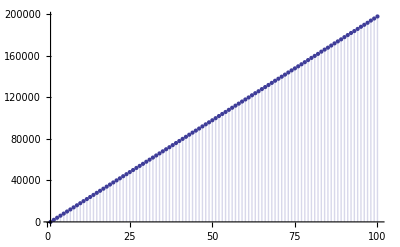

```mathematica
DiscretePlot[E2pt[n,1,1.001,0],{n,1,100}]
```

```mathematica
E2pt[100,1,1.0001,1]
```

-1.9802×10^6

```mathematica
E2pa[n_,k_,a_,s_,m_]:= a^s ( Binomial[k,m]Pochhammer[s+m-k+1,k-1]/Gamma[k]((E2[a^-s n,m,a]+a^m (-1)^(k-m+1)s^(k-1) /Pochhammer[s+m-k+1,k-1])))

E2pa[n,1,a,s,0]
E2pa[n,1,a,s,1]
```

a^s (1+E2[a^-s n,0,a])

a^s (-a+E2[a^-s n,1,a])

```mathematica
E2pa[n,2,a,s,0]
E2pa[n,2,a,s,1]
E2pa[n,2,a,s,2]
```

a^s (-1+s) (-s/(-1+s)+E2[a^-s n,0,a])

2 a^s s (a+E2[a^-s n,1,a])

a^s (1+s) (-(a^2 s)/(1+s)+E2[a^-s n,2,a])

```mathematica
E2pa[n,3,a,s,0]
E2pa[n,3,a,s,1]
E2pa[n,3,a,s,2]
E2pa[n,3,a,s,3]
```

1/2 a^s (-2+s) (-1+s) (s^2/((-2+s) (-1+s))+E2[a^-s n,0,a])

3/2 a^s (-1+s) s (-(a s)/(-1+s)+E2[a^-s n,1,a])

3/2 a^s s (1+s) ((a^2 s)/(1+s)+E2[a^-s n,2,a])

1/2 a^s (1+s) (2+s) (-(a^3 s^2)/((1+s) (2+s))+E2[a^-s n,3,a])

```mathematica
E2pa[n,4,a,s,0]
E2pa[n,4,a,s,1]
E2pa[n,4,a,s,2]
E2pa[n,4,a,s,3]
E2pa[n,4,a,s,4]
```

1/6 a^s (-3+s) (-2+s) (-1+s) (-s^3/((-3+s) (-2+s) (-1+s))+E2[a^-s n,0,a])

2/3 a^s (-2+s) (-1+s) s ((a s^2)/((-2+s) (-1+s))+E2[a^-s n,1,a])

a^s (-1+s) s (1+s) (-(a^2 s^2)/((-1+s) (1+s))+E2[a^-s n,2,a])

2/3 a^s s (1+s) (2+s) ((a^3 s^2)/((1+s) (2+s))+E2[a^-s n,3,a])

1/6 a^s (1+s) (2+s) (3+s) (-(a^4 s^3)/((1+s) (2+s) (3+s))+E2[a^-s n,4,a])

```mathematica
a^s(-1+s)(-s/(-1+s)+1)
```

```mathematica
FullSimplify[a^s (-1+s) (1-s/(-1+s))]
```

-a^s

```mathematica
(-1+s)(-s/(-1+s)+1)
```

(-1+s) (1-s/(-1+s))

```mathematica
a^s ((-1+s)-(s(-1+s))/(-1+s))
```

-a^s

```mathematica
FullSimplify[2a^s s(a+Sum[1,{j,2,Floor[n/(a^s)]}]-a Sum[ 1, {j,1,Floor[n/(a^(s+1))]}])]
```

2 a^s s (-1+a-a Floor[a^(-1-s) n]+Floor[a^-s n])

```mathematica
FullSimplify[2 a^s s (-1+a-a (a^(-1-s) n-1)+(a^-s n-1))]
```

4 (-1+a) a^s s